# Nematic fluids of discs mixed with shape-persistent living polymers

## Initialization

```mathematica
Clear["Global`*"]
```

Define some fixed parameters:

```mathematica
(*eb=1;
qq = (1+√(1+4*4*Exp[-eb]))/2;
zz = ((1+√(1+4*4*Exp[-eb]))/2)^2;*)
ratio = 100;
qq=1;(*ratio/4;*)
zz=1 ;(*Pi*qq;*)
precision=20;
cutoff = 10^-5;
```

Definition of functions:

```mathematica
(* alignment amplitudes *)

ar=(5/4)*(rrn*srav-2*qq*rdn*sd);
ad=(5/4)*(zz*rdn*sd-2*qq*rrn*srav);

(* chi parameter for weakly flexible  rods *)

xi=1+Abs[ar]+lp-√(1+2*lp+2*Abs[ar]*lp+lp^2);
(* effective amplitude *)

arbar=ar-Sign[ar]*xi;
(* polymer length distribution *)
rln[ll_]:=ll*Exp[eb+lambda*ll]*Exp[arbar*ll]*DawsonF[√((3*arbar*ll)/2)]/(√((3*arbar*ll)/2));
(* nematic order parameters *)
srl[ll_]:=If[Abs[DawsonF[√((3*arbar*ll)/2)]]<cutoff,
-1/2 (1+1/(arbar*ll)-1/(√(2*arbar*ll/3) 1/(2 √((3*arbar*ll)/2))+1/(4(√((3*arbar*ll)/2))^3)+3/(8(√((3*arbar*ll)/2))^5))),
-1/2 (1+1/(arbar*ll)-1/(√(2*arbar*ll/3) DawsonF[√((3*arbar*ll)/2)]))];
sdf:=-1/2 (1+1/ad+1/(√(2*ad/3) DawsonF[√((3*ad)/2)]));
```

## Polymer Distributions in the Nematic Phase

Equation system to obtain OverBar[S_r], S_d and λ:

```mathematica
solveConditions[lp_, eb_,rrn_,rdn_,llmax_, sravs_, sds_, lambdas_]:=FindRoot[{
Sum[rln[ll],{ll,1,llmax}]==rrn,
rrn^-1*Sum[srl[ll]*rln[ll],{ll,1,llmax}]==srav,
sdf==sd
},{{lambda,lambdas},{srav,sravs},{sd,sds}}, MaxIterations:>200 ];
```

### Writing solutions to files

```mathematica
llmax=250;
ss=-0.49387383195943035;
sss=0.7712292286952386;
lambdas=-2.717600572715607;
dir=CreateDirectory["~/RodsAndDisks/P2-distributions/" ]
Do[
sravs=ss;
sds=sss;
If[FileExistsQ["~/RodsAndDisks/P2-distributions/_" <>ToString[N[qq]]<>"_"<>ToString[N[zz]]<>"_"<>ToString[lp]<>"_"<>ToString[eb]<>"_"<>ToString[xx]<>"_"<>ToString[cc]<>"_.dat"],
Print["File already exists"],

Print["Creating new file"];
rrn=cc*(1-xx);
rdn=cc*xx;
solv1 = {lambda,srav, sd}/.solveConditions[lp, eb, rrn, rdn, llmax, sravs, sds, lambdas];
lambda=Re[solv1[[1]]];
srav=Re[solv1[[2]]];
sd=Re[solv1[[3]]];
Print[cc, " ", lambda, " ", srav, " ", sd];
(* write polymer distribution to file *)
out = {lambda,srav,sd};
Export[CreateFile["~/RodsAndDisks/P2-distributions/_" <>ToString[N[qq]]<>"_"<>ToString[N[zz]]<>"_"<>ToString[lp]<>"_"<>ToString[eb]<>"_"<>ToString[xx]<>"_"<>ToString[cc]<>"_.txt"],out];
resp={};
For[ii=1,ii<llmax,ii=ii+1;
AppendTo[resp,{ii,Re[rln[ii]]}];
];
Export[CreateFile["~/RodsAndDisks/P2-distributions/_" <>ToString[N[qq]]<>"_"<>ToString[N[zz]]<>"_"<>ToString[lp]<>"_"<>ToString[eb]<>"_"<>ToString[xx]<>"_"<>ToString[cc]<>"_.dat"],resp]
];,
{cc,{5}},
{eb,{-5}},
{lp,{5}},
{xx,{0.95}}
];
```

CreateDirectory::filex: /home/marina/RodsAndDisks/P2-distributions/ already exists.

$Failed

Creating new file

General::munfl: Exp[-780.776] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-775.654] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1217.15] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

5 -1.09465 -0.483826 0.220823

### Plot from files

```mathematica
files=FileNames["*.dat","~/RodsAndDisks/P2-distributions/"];
dir=CreateDirectory["~/RodsAndDisks/P2-distributions/plots/" ]
Do[
dis = Import[filename,"Table"];
filename=Last[FileNameSplit[filename]];
param = StringSplit[filename,"_"];
qq=param[[2]];
zz=param[[3]];
lp=param[[4]];
eb=param[[5]];
xx=param[[6]];
cc=param[[7]];
Export[
"~/RodsAndDisks/P2-distributions/plots/_" <>ToString[N[qq]]<>"_"<>ToString[N[zz]]<>"_"<>ToString[lp]<>"_"<>ToString[eb]<>"_"<>ToString[xx]<>"_"<>ToString[cc]<>"_.png",ListPlot[Take[dis,80], PlotLabel->"q="<>ToString[qq]<>", z="<>ToString[zz]<>", lp="<>ToString[lp]<>", eb="<>ToString[eb]<>", x="<>ToString[xx]<>", c="<>ToString[cc], PlotRange->Full]
];,
{filename,files}
];
```

/home/marina/RodsAndDisks/P2-distributions/plots/

### Parameter interpolations in terms of the concentration

```mathematica
lp=5;
eb=1;
llmax=150;
sravs=0.326926896;
sds=-0.2392626328;
lambdas=-1.2931899;
xx=0.01;
lambdad={};
sravd={};
sdd={};
For[cc=2,cc<5.5,cc=cc+0.1;
rrn=cc*(1-xx);
rdn=cc*xx;
solv1 = {lambda,srav, sd}/.solveConditions[lp, eb, rrn, rdn, llmax, sravs, sds, lambdas];
lambdan=Re[solv1[[1]]];
sravn=Re[solv1[[2]]];
sdn=Re[solv1[[3]]];
AppendTo[lambdad,{cc,lambdan}];
AppendTo[sravd,{cc,sravn}];
AppendTo[sdd,{cc,sdn}];
Print[cc, " ", lambdan, " ", sravn, " ", sdn];
sravs=sravn;
sds=sdn;
lambdas=lambdan;

];
lambdaInterp=Interpolation[lambdad];
sravInterp=Interpolation[sravd];
sdInterp=Interpolation[sdd];
Plot[{lambdaInterp[c], sravInterp[c], sdInterp[c]}, {c,2.1,5.5}]
```

## Isotropic-Nematic phase transition

Functions for the chemical potential and the pressure:

```mathematica
wur[ll_]:=-3/2*((arbar*ll)^2+2*arbar*ll)*srl[ll];

wud[ll_]:=3/4*(arbar*ll)^2+(3/2*(arbar*ll)^2-3*arbar*ll)*srl[ll];

sigmarod[ll_]:=-Log[Exp[SetPrecision[arbar*ll,precision]]*DawsonF[SetPrecision[√((3*arbar*ll)/2),precision]]/(√(3/2*arbar*ll))]+ arbar*ll*srl[ll];

sigmadisk=-Log[Exp[SetPrecision[ad,precision]]*DawsonF[SetPrecision[√((3*ad)/2),precision]]/(√(3/2*ad))]+ad*sd;

rli[ll_]:=ll*Exp[eb]*(1-SetPrecision[2/(1+√(1+4*rri*Exp[-eb])),precision])^ll;

muriso=  2*rri+2*qq*rdi+Sum[rli[ll]/(ll*rri)*(Log[rli[ll]/ll]-eb),{ll, 1,llmax}];

(*murnem [lp_, eb_, rrn_, rdn_, srav_, sd_, lambda_, llmax_]:=2*rrn*(1-5/8*srav^2)+2*qq*rdn*(1+5/4*srav*sd)+Sum[rl[lp, eb, rrn, rdn, srav, sd, lambda, ll]/(ll*rrn)*(Log[rl[lp, eb, rrn, rdn, srav, sd, lambda, ll]/ll]+sigmarod[lp, rrn, rdn, srav, sd,ll]-eb-2*ll/(3*lp)*Which[(rdn/(rrn+rdn))<0.5,wur[lp, rrn, rdn, srav, sd,ll],(rdn/(rrn+rdn))>=0.5,wud[lp, rrn, rdn, srav, sd, ll]]),{ll, 1,llmax}];*)
murnem =2*rrn*(1-5/8*srav^2)+2*qq*rdn*(1+5/4*srav*sd)+Sum[rln[ll]/(ll*rrn)*(Log[rln[ll]/ll]+sigmarod[ll]-eb-2*ll/(3*lp)*wur[ll]),{ll, 1,llmax}];

mudiso=Log[rdi]+2*zz*rdi+2*qq*rri;

mudnem=Log[rdn]+sigmadisk+2*zz*rdn*(1-5/8*sd^2)+2*qq*rrn*(1+5/4*srav*sd);

pressureiso=Sum[rli[ll]/ll,{ll,1,llmax}]+rdi+rri^2+2*qq*rri*rdi+zz*rdi^2;

pressurenem=Sum[rln[ll]/ll,{ll,1,llmax}]+rdn+rrn^2*(1-5/8 srav^2)+2*qq*rrn*rdn*(1+5/4*srav*sd)+zz*rdn^2*(1-5/8*sd^2);
```

Equation system to obtain OverBar[S_r], S_d, λ, c_i, c_n, x_n:

```mathematica
solveConditions2[lp_, eb_,llmax_, sravs_, sds_, lambdas_, rri_, rrns_, rdis_, rdns_]:=(n=0;
FindRoot[{
Sum[rln[ll],{ll,1,llmax}]==rrn,
rrn^-1*Sum[srl[ll]*rln[ll],{ll,1,llmax}]==srav,
sdf==sd,
muriso==murnem,
mudiso==mudnem,
pressureiso==pressurenem

},{{lambda,lambdas},{srav,sravs,-1,1},{sd,sds,-1,1}, {rrn, rrns,10^-10,15}, {rdi,rdis,10^-10,15}, {rdn,rdns,10^-10,15}},EvaluationMonitor:>(n++;Print[{n}])]);
(*{{lambda,lambdas},{srav,sravs},{sd,sds}, {rrn, rrns}, {rdi,rdis}, {rdn,rdns}},EvaluationMonitor:>(n++;Print[{n}])*)
pressure [lp_, eb_,llmax_, sravs_, sds_, lambdas_, xxns_, ccis_, ccns_, xxi_]:= (
rri=ccis*(1-xxi);
rdis=ccis*xxi;
rrns=ccns*(1-xxns);
rdns=ccns*xxns;
solv2 = {lambda,srav, sd, rrn,rdi,rdn}/.solveConditions2[lp, eb, llmax, sravs, sds, lambdas, rri, rrns, rdis, rdns];
lambda=Re[solv2[[1]]];
srav=Re[solv2[[2]]];
sd=Re[solv2[[3]]];
rrn=Re[solv2[[4]]];
rdi=Re[solv2[[5]]];
rdn=Re[solv2[[6]]];
xxnn=rdn/(rrn+rdn);
ccin=rri+rdi;
ccnn=rrn+rdn;
{xxi, pressureiso,xxnn,pressurenem,lambda, srav,sd,ccin,ccnn}
)
```

### Plot

```mathematica
lp=5;
eb=-1;
llmax=150;
sravs=0.5;
sds=-0.5;
lambdas=-2;
xxi=0.2;
xxns=0.2;
ccis=3.2;
ccns=3.2;
(*Plot[pressure [lp, eb,llmax, sravs, sds, lambdas, xxns, ccis, ccns, xxi][[2]], {xxi,0.01,0.99},PlotPoints->4, PlotRange->Full]*)
pressure[lp, eb,llmax, sravs, sds, lambdas, xxns, ccis, ccns, xxi]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.2,6.88669,9.52808×10^-6,4.71826,-1.2419,0.45498,-0.441412,2.56002,2.32023}

#### Limit situations

x = 0 -> Pure rods

```mathematica
rdi=0;
rdn=0;
sd=0;
lp=5;
eb=1;
sravs=0.5;
lambdas=-2.5;
ccis=1;
ccns=2;
solveConditions4[lp_, eb_,sravs_, lambdas_, rris_, rrns_]:=(n=0;
FindRoot[{
-(ⅇ^eb (√3 √arbar (arbar-2 lambda)+2 (-arbar-lambda)^(3/2) √(2-(3 arbar)/(arbar+lambda)) ArcSinh[(√(3/2) √arbar)/(√(-arbar-lambda))]))/(√3 √arbar (arbar-2 lambda)^2 (arbar+lambda))==rrn,
rrn^-1*(ⅇ^eb (-3 √arbar lambda+(2 √3 √(-arbar-lambda) (-arbar+lambda) ArcSinh[(√(3/2) √arbar)/(√(-arbar-lambda))])/(√(2-(3 arbar)/(arbar+lambda)))))/(3 arbar^(3/2) (arbar-2 lambda) (arbar+lambda))==srav,
muriso==murnem,
pressureiso==pressurenem

},{{lambda,lambdas},{srav,sravs,-1,1},{rri, rris,10^-10,15}, {rrn,rrns,10^-10,15}},EvaluationMonitor:>(n++;Print[{n, sd, lambda, srav, rri, rrn}])]);
rris=ccis;
rrns=ccns;
solv2 = {lambda,srav, rri, rrn}/.solveConditions4[lp, eb, sravs,lambdas, rris, rrns]
lambda=Re[solv2[[1]]];
srav=Re[solv2[[2]]];
rri=Re[solv2[[3]]];
rrn=Re[solv2[[4]]];
ccin=rri;
ccnn=rrn;
{0, pressureiso,0,pressurenem,lambda, srav,ccin,ccnn}
Clear[lambda,srav,rri,rrn]
```

{-1.21563,-6.79318×10^-9,1.62875,1.62875}

{0,3.79861,0,3.79861+0. ⅈ,-1.21563,-6.79318×10^-9,1.62875,1.62875}

x = 1 -> Pure disks

```mathematica
rri=0;
rrn=0;
srav=0;
pressureiso=rdi+rri^2+2*qq*rri*rdi+zz*rdi^2;

pressurenem=rdn+rrn^2*(1-5/8 srav^2)+2*qq*rrn*rdn*(1+5/4*srav*sd)+zz*rdn^2*(1-5/8*sd^2);
lp=5;
eb=1;
sds=0.8;
ccis=6;
ccns=3;
solveConditions5[lp_, eb_,sds_, rdis_, rdns_]:=(n=0;
FindRoot[{
sdf==sd,
mudiso==mudnem,
pressureiso==pressurenem

},{{sd,sds,-1,1},{rdi, rdis,10^-10,15}, {rdn,rdns,10^-10,15}},EvaluationMonitor:>(n++;Print[{n, srav, sd, rdi, rdn}])]);
rdis=ccis;
rdns=ccns;
solv2 = {sd, rdi, rdn}/.solveConditions5[lp, eb, sds,rdis, rdns]
sd=Re[solv2[[1]]];
rdi=Re[solv2[[2]]];
rdn=Re[solv2[[3]]];
ccin=rdi;
ccnn=rdn;
{0, pressureiso,0,pressurenem,sd,ccin,ccnn}
Clear[sd,rdi,rdn]
```

{0.57351,3.50438,3.87238}

{0,15.7851,0,15.7851,0.57351,3.50438,3.87238}

## Draft/Tests

### With the While-Loop:

```mathematica
solveConditions3[lp_, eb_,llmax_, srav_, sd_, lambda_, rri_, rrns_, rdis_, rdns_]:=FindRoot[{

muriso[eb, rri, rdi, llmax]==murnem[lp, eb, rrn, rdn, srav, sd, lambda, llmax],
mudiso[rri,rdi]==mudnem[lp,rrn, rdn, srav, sd],
pressureiso[eb, rri,rdi, llmax]==pressurenem[lp, eb, rrn, rdn, srav, sd, lambda, llmax]

},{{rrn, rrns,10^-5,10}, {rdi,rdis,10^-5,10}, {rdn,rdns,10^-5,10}}];
```

```mathematica
lp=5;
eb=1;
llmax=150;
sravs=0.8624569216635748;
sds=-0.40577124411248866;
lambdas=-2.9689877260665503;
xxi=0.1;
xxns=0.01;
ccis=3.6029484239166867;
ccns=3.9801539278678573;
rri=ccis*(1-xxi);
rdis=ccis*xxi;
rrns=ccns*(1-xxns);
rdns=ccns*xxns;
df=100;

While[df>1,
solv2 = {lambda,srav, sd}/.solveConditions[lp, eb,rrns,rdns,llmax, sravs, sds, lambdas];
lambdan=Re[solv2[[1]]];
sravn=Re[solv2[[2]]];
sdn=Re[solv2[[3]]];
Print[lambdan, sravn, sdn];

solv3 = {rrn,rdi,rdn}/.solveConditions3[lp, eb,llmax, sravn, sdn, lambdan, rri, rrns, rdis, rdns];
rrnn=Re[solv3[[1]]];
rdin=Re[solv3[[2]]];
rdnn=Re[solv3[[3]]];
df=10^5*Max[{Abs[sravs-sravn],Abs[sds-sdn],Abs[lambdas-lambdan],Abs[rdis-rdin],Abs[rrns-rrnn],Abs[rdns-rdnn]}];
sravs=sravn;
sds=sdn;
lambdas=lambdan;
rdis=rdin;
rrns=rrnn;
rdns=rdnn;
Print[df]
];
xxnn=rdnn/(rrnn+rdnn);
ccin=rri+rdin;
ccnn=rrnn+rdnn;
{xxi, pressureiso[eb, rri,rdin, llmax],xxnn,pressurenem[lp, eb, rrnn, rdnn, sravn, sdn, lambdan, llmax]}
{lambdan, sravn, sdn, xxnn, ccin, ccnn}
```

3.18084×10^-10

{0.1,129.707,0.914818,130.223}

{-1.54902,3.04968×10^-9,-8.57716×10^-10,0.914818,10.9583,10.9311}

### Others

```mathematica
Integrate[Exp[a*x^2]*Sin[x], {x, 0, Pi}]
```

(ⅇ^(1/4/a) √π (-2 Erf[1/(2 √a)]+Erf[(1-2 ⅈ a π)/(2 √a)]+Erf[(1+2 ⅈ a π)/(2 √a)]))/(4 √a)

```mathematica
DawsonF[√((3*arbar[5, 3, 3, 0.8, -0.3]*143)/2)]
```

General::munfl: Exp[-730.897] is too small to represent as a normalized machine number; precision may be lost.

0.0185071

```mathematica
DawsonF[SetPrecision[√((3*arbar[5, 3, 3, 0.8, -0.3]*143)/2),20]]
```

0.01850715269772228

```mathematica
(1.000000082740371*^-10)^-1*Sum[srl[5,1.000000082740371*^-10, 6.403333933053428, 0.8635690936310091, -0.327170864745854, ll]*rl[5, 1, 1.000000082740371*^-10, 6.403333933053428, 0.8635690936310091, -0.327170864745854, -4.765905785346516, ll],{ll,1,150}]
```

7.23822×10^8

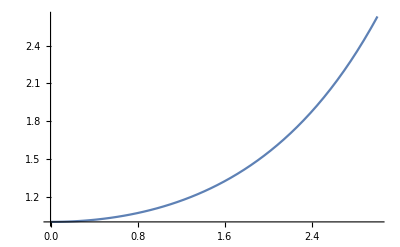

```mathematica
s=Exp[x]*DawsonF[√((3*x)/2)]/√((3*x)/2);
Plot[s,{x,0,3}]
```

```mathematica
(2/(1+√(1+4*4*Exp[-1])))^-1
```

1/2 (1+√(1+16/ⅇ))

```mathematica
N[1/2 (1+√(1+16/ⅇ))]
```

1.81207

```mathematica
(*Subscript[ϵ, b]=1;
λ = -2.7;
α = 2.6;*)
y[x_]=1/(2x)+1/(4 x^3)+3/(8 x^5)
∑_(l=1)^∞ l*ⅇ^(eb+l*λ)ⅇ^(α*l)y[√((3α*l)/2)]/(√((3α*l)/2))
```

3/(8 x^5)+1/(4 x^3)+1/(2 x)

-(ⅇ^eb (3 ⅇ^(α+λ) α^2-α Log[1-ⅇ^(α+λ)]+ⅇ^(α+λ) α Log[1-ⅇ^(α+λ)]+PolyLog[2,ⅇ^(α+λ)]-ⅇ^(α+λ) PolyLog[2,ⅇ^(α+λ)]))/(9 (-1+ⅇ^(α+λ)) α^3)

```mathematica
∑_(l=1)^∞ l*ⅇ^eb(1-2/(1+√(1+4*Subscript[ρ, r]*Exp[-eb])))^l
```

ρ_r

```mathematica
Subscript[ϵ, b]=1;
λ = -2.7;
α = 2.6;
Plot[l*ⅇ^(Subscript[ϵ, b]+l*λ)ⅇ^(α*l)DawsonF[√((3α*l)/2)]/(√((3α*l)/2)), {l,1,50}]
```

```mathematica
(* Dawson function approximation:
http://www.scielo.org.mx/scielo.php?script=sci_arttext&pid=S0188-62662019000100175&lng=es&nrm=iso*)
```

```mathematica
∫_0^∞ l*ⅇ^(eb+l*λ)ⅇ^(α*l)DawsonF[√((3α*l)/2)]/(√((3α*l)/2))ⅆl
```

ConditionalExpression[-(ⅇ^eb (√3 √α (α-2 λ)+2 (-α-λ)^(3/2) √(2-(3 α)/(α+λ)) ArcSinh[(√(3/2) √α)/(√(-α-λ))]))/(√3 √α (α-2 λ)^2 (α+λ)), Re[-α/2+λ]<0&&Re[α+λ]<0]

```mathematica
∫_0^∞ 1/4 (-2-2/(α*l)+(√6)/(√(α*l)* DawsonF[√((3*α*l)/2)]))*l*ⅇ^(eb+l*λ)ⅇ^(α*l)DawsonF[√((3α*l)/2)]/(√((3α*l)/2))ⅆl
```

ConditionalExpression[-(ⅇ^eb (-3 √α λ+(2 √3 √(-α-λ) (-α+λ) ArcSinh[(√(3/2) √α)/(√(-α-λ))])/(√(2-(3 α)/(α+λ)))))/(3 α^(3/2) (α-2 λ) (α+λ)), Re[-α/2+λ]<0&&Re[α+λ]<0]